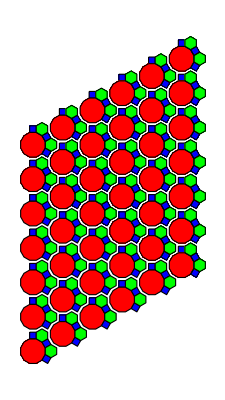

```mathematica
dodeca=Polygon[(Table[2{Sin[θ-2 Pi/24],Cos[θ-2 Pi/24]},{θ,0,2 Pi-2 Pi/12,2Pi/12}]//Simplify)];
square1=Polygon[({{-1,1},{1,1},{1,-1},{-1,-1}}+Array[{0,1}&,4])√2 (-1+√3)/2+Array[{0,(1+√3)/(√2)}&,4]];
hexa=Polygon[{{-√2,√2},{-√(2-√3),√(2+√3)},{-√(2-√3),√(14-3 √3)},{-√2,√(26-8 √3)},{(-5+√3)/(√2),√(14-3 √3)},{(-5+√3)/(√2),√(2+√3)}}];
rotate[g_,q_]:=GeometricTransformation[g,RotationTransform[q]];
translate[g_,t_]:=GeometricTransformation[g,TranslationTransform[t]];
fundamental={Red,dodeca,Blue,Table[rotate[square1,2 Pi k/6],{k,-2,0}],Green,Table[rotate[hexa,2 Pi k/6],{k,-2,-1}]};
ω1={0,2 √6};
ω2={3 √2,√6};

Graphics[{EdgeForm[Thick],Table[translate[fundamental,1.1 n1 ω1+1.1n2 ω2],{n1,-3,3},{n2,-3,2}]},PlotRange->10]
```

```mathematica
Polygon
```

Polygon

```mathematica
Head[fundamental[[2]]]//FullForm
```

Polygon

```mathematica
Mean[{{1,2},{3,4}}]
```

{2,3}

```mathematica
fundamental[[2,1]]//Mean
```

{0,0}

```mathematica
explodedTesselation
```

```mathematica
RGBColor[1., 0., 0.]//FullForm
```

RGBColor[1.,0.,0.]

```mathematica
randomFunction[y_]:=RandomReal[{-1,1}]+y/100.0;
randomFunction[-50]
```

-0.984881

{RGBColor[0.6, 0.6, 0.65],RGBColor[0.4, 0.4, 0.54],RGBColor[0.5, 0.5, 0.54],RGBColor[0.6, 0.6, 0.65],RGBColor[0.4, 0.4, 0.54],22361,Polygon[{{152.217,268.002},{153.253,268.002},{153.253,266.967},{152.217,266.967}}],RGBColor[0.5, 0.5, 0.54],Polygon[{{155.233,265.063},{155.233,264.027},{156.129,263.51},{157.026,264.027},{157.026,265.063},{156.129,265.58}}],Polygon[{{153.536,266.967},{154.432,266.449},{155.329,266.967},{155.329,268.002},{154.432,268.52},{153.536,268.002}}]}
 |  |  |  |

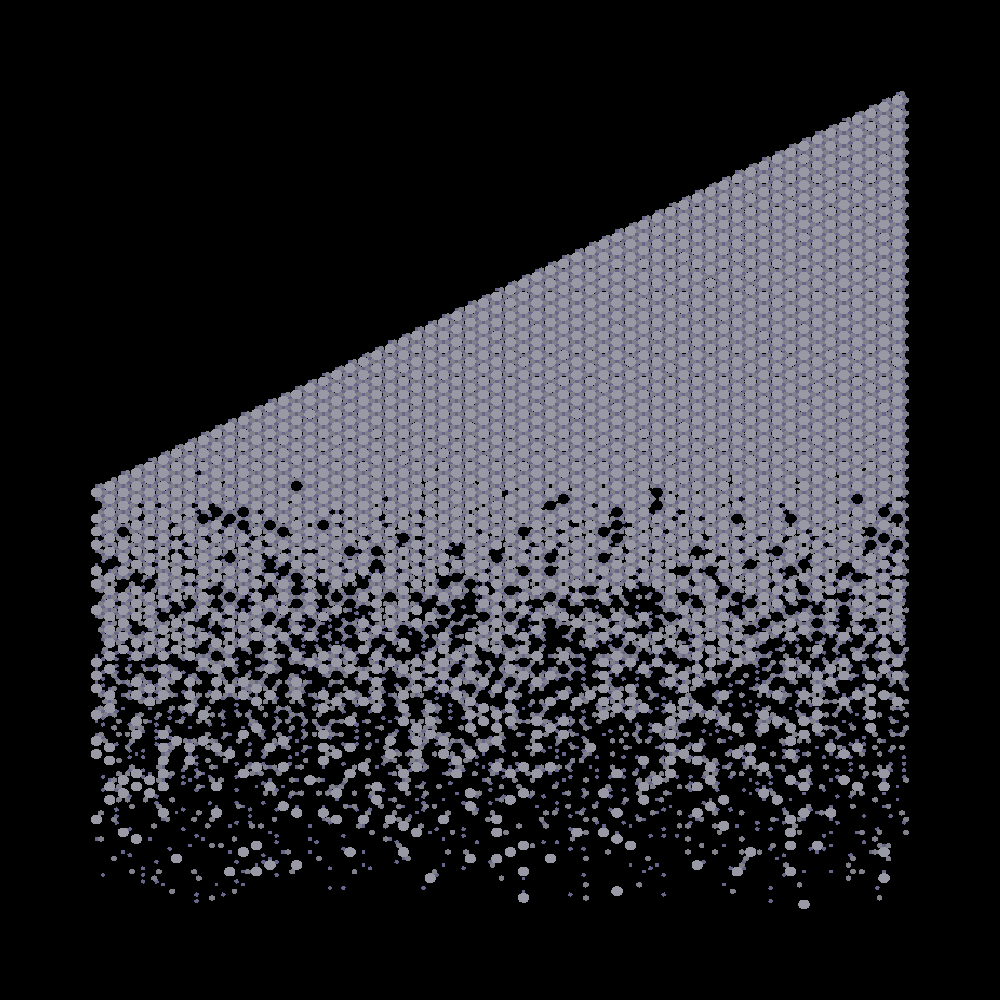

```mathematica
plainified=Flatten[fundamental/.{GeometricTransformation[Polygon[list_],{mat_,trs_}]:>Polygon[(N@(mat.#+trs)&/@list)]}];
tesselation=Flatten[Table[plainified/.{Polygon[list_]:> Polygon[(#+n1 ω1+n2 ω2)&/@list]},{n1,-30,30},{n2,-30,30}]];
explodedTesselation=tesselation/.{Polygon[list_]:>Polygon[(#-Mean[list])+1.2 Mean[list]&/@list  ]};
replacedColors=explodedTesselation/.{Red->RGBColor[0.6,0.6,0.65],Green->RGBColor[0.5,0.5,0.54],Blue->RGBColor[0.4,0.4,0.54]};
dropRandom=Select[replacedColors,(Head[#]==RGBColor) ||randomFunction[ Mean[#[[1]]][[2]]] >0&]
Graphics[dropRandom,PlotRange->100,Background->Black,ImageSize->{1000,1000}]
```

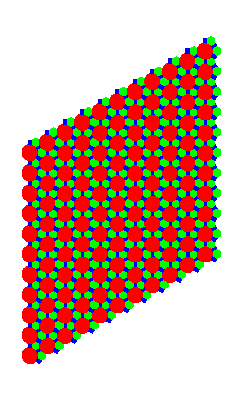

```mathematica
Graphics[tesselation]
```

```mathematica
fundamental[[4]]
```

{GeometricTransformation[Polygon[{{-(-1+√3)/(√2),√2 (-1+√3)+(1+√3)/(√2)},{(-1+√3)/(√2),√2 (-1+√3)+(1+√3)/(√2)},{(-1+√3)/(√2),(1+√3)/(√2)},{-(-1+√3)/(√2),(1+√3)/(√2)}}],{{{-1/2,(√3)/2},{-(√3)/2,-1/2}},{0,0}}],GeometricTransformation[Polygon[{{-(-1+√3)/(√2),√2 (-1+√3)+(1+√3)/(√2)},{(-1+√3)/(√2),√2 (-1+√3)+(1+√3)/(√2)},{(-1+√3)/(√2),(1+√3)/(√2)},{-(-1+√3)/(√2),(1+√3)/(√2)}}],{{{1/2,(√3)/2},{-(√3)/2,1/2}},{0,0}}],GeometricTransformation[Polygon[{{-(-1+√3)/(√2),√2 (-1+√3)+(1+√3)/(√2)},{(-1+√3)/(√2),√2 (-1+√3)+(1+√3)/(√2)},{(-1+√3)/(√2),(1+√3)/(√2)},{-(-1+√3)/(√2),(1+√3)/(√2)}}],{{{1,0},{0,1}},{0,0}}]}

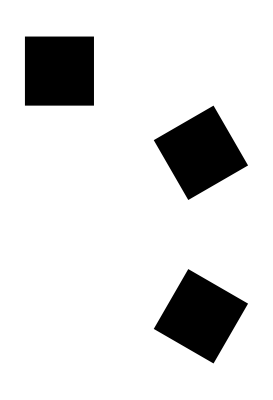

```mathematica
Graphics[fundamental[[4]]]
```